# Introducción al cómputo

## Métodos numéricos

## ¿Qué es el cómputo?

En esencia es un proceso que nos permite razonar sobre el mundo.

### Ejemplo: Hueso de Ishango

Su antiguedad se estima en 20,000 años

### Ábaco

## El concepto de número

La mayoría de las personas poseemos una noción intuitiva del concepto de número.

### Formulación axiomática

## Representación binaria

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics-,-Graphics-
```

## Operaciones lógicas

```mathematica
Map[Labeled[VisualizeGate[#],#,Top]&,{BitAnd,BitOr,BitXor}]
```

{A | B | Result
0 | 0 | 0
0 | 1 | 0
1 | 0 | 0
1 | 1 | 1BitAnd,A | B | Result
0 | 0 | 0
0 | 1 | 1
1 | 0 | 1
1 | 1 | 1BitOr,A | B | Result
0 | 0 | 0
0 | 1 | 1
1 | 0 | 1
1 | 1 | 0BitXor}

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics--Graphics-
```

## Aritmética a partir de operaciones lógicas

Half adder: Implementa una semisuma

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

```mathematica
PlotCompactInteractiveSystem[HalfAdder[a0,b0],ImageSize->200]
```

## Aritmética a partir de operaciones lógicas

Full adder: Permite sumar con un carry

```mathematica
VisualizeAdder[FullAdder,3,"Carry"]
```

A | B | C | Carry | Result
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1

```mathematica
PlotCompactInteractiveSystem[FullAdder[a0,b0,c0],ImageSize->300]
```

```mathematica
Aritmética a partir de operaciones lógicas
```

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUAdder,Transpose[pairs]];
labels = {"A","B","Carry","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Carry | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 0 | {0,1}
{0,0} | {1,0} | 0 | {1,0}
{0,0} | {1,1} | 0 | {1,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {1,0}
{0,1} | {1,0} | 0 | {1,1}
{0,1} | {1,1} | 1 | {0,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {1,1}
{1,0} | {1,0} | 1 | {0,0}
{1,0} | {1,1} | 1 | {0,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 1 | {0,0}
{1,1} | {1,0} | 1 | {0,1}
{1,1} | {1,1} | 1 | {1,0}

```mathematica
PlotCompactInteractiveSystem[ALUAdder[{a1,a2,a3},{b1,b2,b3}]]
```

## Circuito de operaciones aritméticas

```mathematica
aluOpcodes
```

{Add→{0,0,0},Substract→{0,0,1},Increment→{0,1,0},Decrement→{0,1,1},Pass→{1,0,0}}

```mathematica
PlotCompactInteractiveSystem[
Values[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6,
"ShowLabels"->None
]
```

## CPU Completa

```mathematica
Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]]
```

Positive:  | 0
Negative:  | 0
Zero:  | 0
NotZero:  | 0
Parity:  | 0ALU Status | Register A | Register B
00000000 | 00000000
Instruction Register | Address Register
Opcode | Parameter
00000000 | 00000000
LoadA | 0 | 00000000
Ram Read-Enable:  | 0
Ram Write-Enable:  | 0
Stack Read-Enable:  | 0
Stack Write-Enable:  | 0
RegisterA Read-Enable:  | 0
RegisterA Write-Enable:  | 0
RegisterB Write-Enable:  | 0
Jump:  | 0
JumpPos:  | 0
JumpNeg:  | 0
JumpZero:  | 0
JumpNotZero:  | 0
ALU Instruction:  | 0
ALU Opcode:  | Add
Print Enable:  | 0
Halt:  | 0CU Status | Stack Pointer Register
00000000
Stack level | Binary value | Decimal value
1 | {0,0,0,0,0,0,0,0} | 0
2 | {0,0,0,0,0,0,0,0} | 0
3 | {0,0,0,0,0,0,0,0} | 0
4 | {0,0,0,0,0,0,0,0} | 0
5 | {0,0,0,0,0,0,0,0} | 0
6 | {0,0,0,0,0,0,0,0} | 0
7 | {0,0,0,0,0,0,0,0} | 0
8 | {0,0,0,0,0,0,0,0} | 0StackCPU

Lenguaje ensamblador: El nivel más bajo

```mathematica
asm = "
SetA 0
Store <n>
LoadA <n>
SetB 10
Substract
JumpZero <L$1>
Print <n>
LoadA <n>
SetB 1
Add
Store $0
SetA $0
Store <n>
Label <L$1>
Return
Declare <n> 0
";
ExecuteCodeInteractive[code,3]
```

## Lenguajes de nivel más alto

```mathematica
-Graphics--Graphics-
```

```mathematica
program = "var n;
procedure count;
begin
   n := 0;
   while n # 10 do
   begin
      n := n + 1;
   end
end

begin
    call count;
    print n
end.";
```

```mathematica
tokens = Tokenize[program,symbolRecognizer,keywordRecognizer];
```

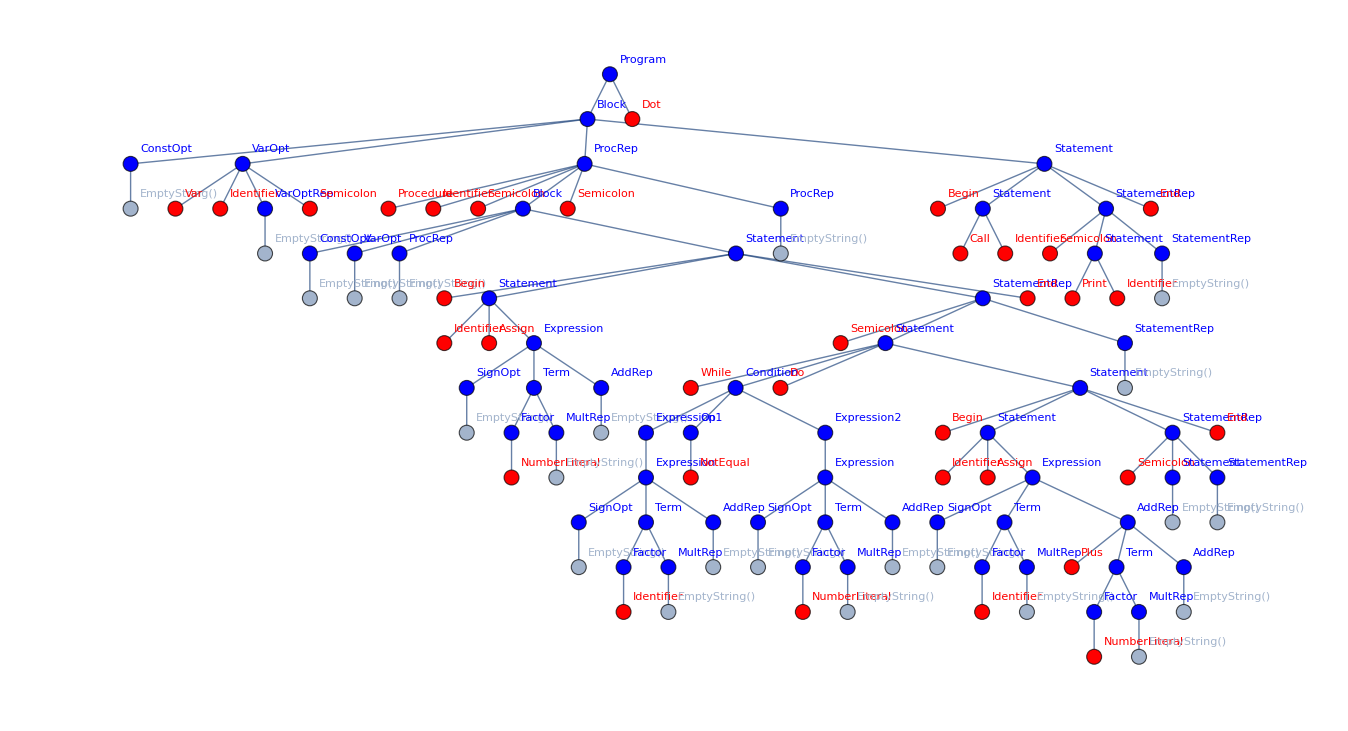

```mathematica
ParseTree[tokens,grammar]
```

```mathematica
CompilePL0ToASM[program]
```

Call <count>
Print <n>
Return
Label <count>
SetA 0
Store <n>
Label <count::0::L1>
SetA 10
LoadB <n>
Substract
JumpZero <count::0::L2>
LoadA <n>
SetB 1
Add
Store <count::$0>
LoadA <count::$0>
Store <n>
Jump <count::0::L1>
Label <count::0::L2>
Return
Declare <count::$0> 0
Declare <n> 0